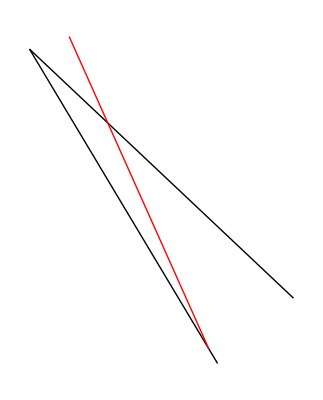

```mathematica
edge1 = Graphics[Line[{{3.45583 ,1.97092},{3.58141, 1.76118}}]];
edge2 = Graphics[Line[{{3.45583, 1.97092},{3.63211,1.80476}}]];
outputtedEdge3 = Graphics[{Red,Line[{{3.57557 ,1.77093},{3.4823 ,1.97931}}]}];
edge3 = Graphics[Line[{{3.58141, 1.76118},{3.63211,1.80476}}]];
checkSegment1 = Graphics[Line[{{3.61468, 1.8158},{4.56288 ,0.232106}}]];
checkSegment2 = Graphics[Line[{{3.49038, 1.96258},{2.7363 ,3.64739}}]];
Show[edge1,edge2,outputtedEdge3]
```

```mathematica
v1 = {3.45583 ,1.97092 ,0.208545};
v2 = {3.57557, 1.77093, 0.134874};
v3 = {3.50812, 1.92163,-0.0227984};
source = {3.50848 ,1.91667,-0.000197482};
target = {3.51597 ,1.91006,-0.0357383};
prospIntersect = {3.51155 ,1.91396,-0.0147716};
```

```mathematica
e1 = Line[{v1,v2}];
e2 = Line[{v1,v3}];
e3 = Line[{v2,v3}];
sourcePt = Point[source];
targetPt =Point[target];
toTarget = Line[{source,target}];
intersectPt = Point[prospIntersect];
edge1 = Graphics3D[e1];
edge2 = Graphics3D[e2];
edge3 = Graphics3D[e3];
drawSourcePt = Graphics3D[{Red,PointSize->.01,sourcePt}];
drawTargetPt = Graphics3D[{Purple,PointSize->.01,targetPt}];
drawIntersectPt = Graphics3D[{Brown,PointSize->.01,intersectPt}];
sourceTargetLine = Graphics3D[{Blue,toTarget}];
Show[edge1,edge2,edge3,drawSourcePt,drawTargetPt,drawIntersectPt,sourceTargetLine]
```

-Graphics3D-

```mathematica
baryVector = {0, 0.0509079 ,0.949092};
prospIntersect = {3.51155 ,1.91396,-0.0147716}
baryWeightsIntersect = baryVector[[1]]*v1+baryVector[[2]]*v2+baryVector[[3]]*v3
baryWeightsIntersect-prospIntersect
```

{3.51155,1.91396,-0.0147716}

{3.51155,1.91396,-0.0147716}

{3.38704×10^-6,-2.01269×10^-6,-2.69482×10^-8}

```mathematica
bSourceWeights = {0.061529, 0.0530631 ,0.885408};
source = {3.50848 ,1.91667,-0.000197482}
baryWeightsSource= bSourceWeights[[1]]*v1+bSourceWeights[[2]]*v2+bSourceWeights[[3]]*v3
```

{3.50848,1.91667,-0.000197482}

{3.50848,1.91667,-0.000197488}